```mathematica
littlewood[n_Integer,x_:x]:=1+Tuples[{1,-1},n]. x^Range[n]
```

```mathematica
littlewood[3]//Column//TraditionalForm
```

x^3+x^2+x+1
-x^3+x^2+x+1
x^3-x^2+x+1
-x^3-x^2+x+1
x^3+x^2-x+1
-x^3+x^2-x+1
x^3-x^2-x+1
-x^3-x^2-x+1

```mathematica
littlewoodRoots[n_]:= ComplexListPlot[x/. Solve[Times @@ littlewood[n]==0, x]]
```

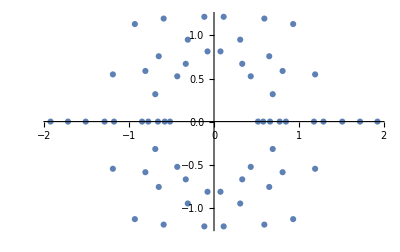

```mathematica
littlewoodRoots[4]
```

#### A fancier function with a slight increase in speed:

```mathematica
showRoots[n_]:=With[{s=Which[n<8,Medium,n<14,Small,True,Tiny],
r=Thread@ParallelMap[NSolveValues[#==0,x]&,littlewood[n]],
o=If[n>12,{ImageSize->1500,Axes->False},{ImageSize->Large}]},
ComplexListPlot@@{r,Sequence@@o,PlotStyle->PointSize@s}];
(* use List@@Last/@NRoots if NSolveValues is not supported *)
```

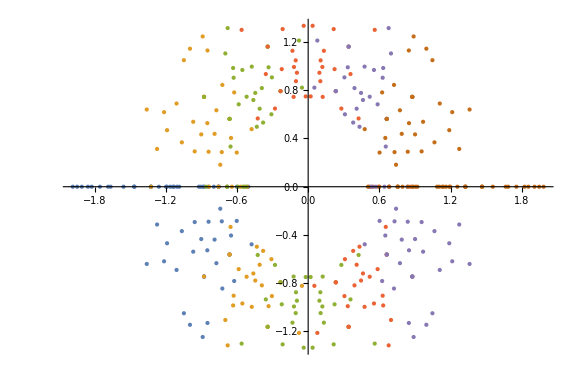

```mathematica
LaunchKernels[];
showRoots[6]
CloseKernels[];
```

```mathematica
fastShowRoots[n_]:=With[{
r=If[n>3,Thread,Identity]@If[n>6,ParallelMap,Map]@##&,
s=AbsolutePointSize@If[n<15,15-n,1/(n-13)],
l=Style["n = "<>ToString@n,FontSize->40],c=2^{1,.5}+.05},
If[n>6 && $KernelCount==0,LaunchKernels[]];
With[{p=r[List@@Last/@NRoots[#==0,x]&,littlewood@n]},
ComplexListPlot@@{p,ImageSize->1500,AspectRatio->Max@Ratios@c,
PlotStyle->s,PlotLabel->l,PlotRange->{-#,#}&/@c,Axes->n<6}]
](* use NSolveValues instead of List@@Last/@NRoots on ver 12.3 *)
```

```mathematica
Do[Export[ToString@n<>".png",fastShowRoots@n],{n,2,15}];
```

```mathematica
Block[{t=Array[Graphics[]&,15]},
Do[t[[i-1]]=fastShowRoots[i],{i,2,Length[t]+1}];
Export["littlewood.gif",t,"DisplayDurations"->1]];
```